High order Ne.b4de.b4lec elements with local complete sequence properties
	Joachim Scho.a8berl and Sabine Zaglmayr

```mathematica
Needs["VectorAnalysis`"]
SetCoordinates[Cartesian[x,y,z]];
```

the Legendrepolynomials       l_i(x)  (i=0,...p)
	l_i(x):=ix

```mathematica
Clear[l]
```

```mathematica
l(i_,x_):=ix;
```

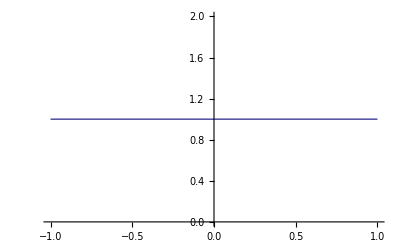
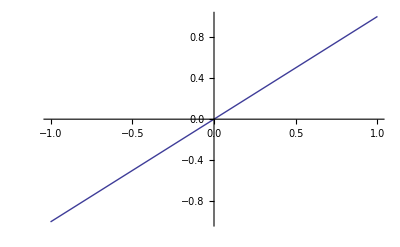
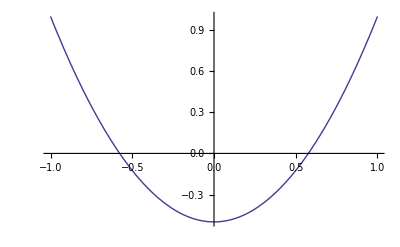
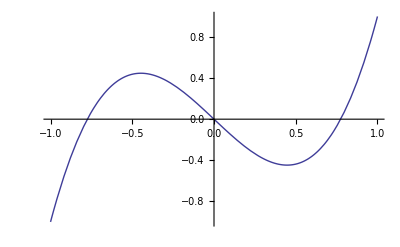
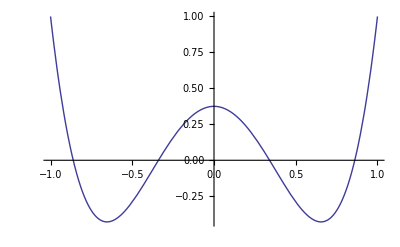
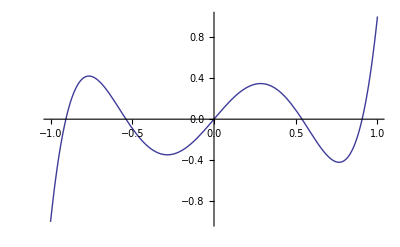

```mathematica
Table[Plot[l[i, x], {x,-1,1}], {i,0,5}]
```

theintegratedLegendre-polynomialsL_i(i=2,...,p)
L_i_[x_]:=∫_-1^x i-1zⅆz

```mathematica
L(i_,x_):=∫_-1^x l(i-1,z)ⅆz
```

```mathematica
For[i=2,i≤6,i++,    L(i,x_)=∫_-1^x l(i-1,z)ⅆz     ]
```

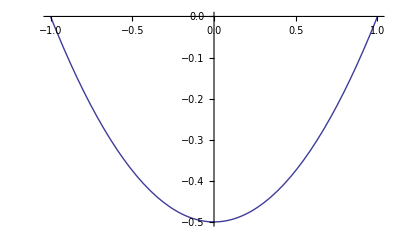
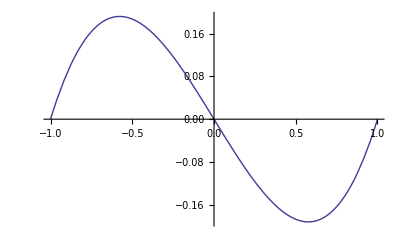
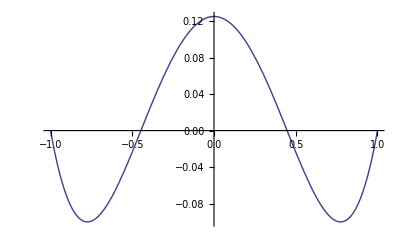
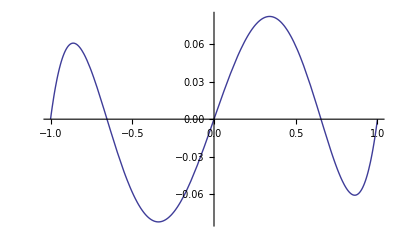

```mathematica
Table[Plot[L(i,x),{x,-1,1}],{i,2,5}]
```

the scaled Legendre polynomials

```mathematica
lS(n_,s_,t_):=Simplify[t^n l(n,s/t)];
```

```mathematica
Table[Plot3D[lS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the scaled integrated Legendre polynomials

```mathematica
LS(n_,s_,t_):=Simplify[t^n L(n,s/t)];
```

```mathematica
Table[Plot3D[LS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,2,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the barycentric coordinates
	λ_i (i=1,2,3,4)

```mathematica
Clear[point, lamda,px, edge,face]
point[0]={0,0,0};  point[1]={1,0,0}; point[2]={0,1,0}; point[3]={0,0,1};
edge[0]={0,1}; edge[1]={0,2};edge[2]={0,3}; edge[3]={1,2}; edge[4]={1,3}; edge[5]={2,3};
face[0]={0,1,2}; face[1]={0,1,3};face[2]={0,2,3};face[3]={1,2,3};

px={0,0,0};
For[i=0,i<4, ++i, px+=point[i]*lamda[i];]
sum=0;
For[i=0,i<4, ++i, sum+=lamda[i]];
px=Append[px, sum];
sol=Solve[px=={x,y,z,1}, {lamda[0],lamda[1], lamda[2], lamda[3]}];
lamda[0]=lamda[0]/.sol[[1]];
lamda[1]=lamda[1]/.sol[[1]];
lamda[2]=lamda[2]/.sol[[1]];
lamda[3]=lamda[3]/.sol[[1]];
```

```mathematica
Clear[lines];
lines={Thick};
For[i=0, i<6, i++,
p1= edge[i][[1]];
p2=edge[i][[2]];
line=Line[ { point[p1] ,point[ p2]  }  ] ;
lines=Append[lines, line];
]
Graphics3D[lines,Axes->True,AxesLabel->{x,y,z}, Boxed->True,ViewVertical->{0,0,1}]
```

-Graphics3D-

```mathematica
G[func_,fac0_]:=Module[{ncf, fac=fac0, cf},
ncf=16;
cf=Table[(-1+2/ncf*(i-1/2))*fac, {i,1,ncf} ];
 ContourPlot3D[func,{x,0,1},{y,0,1},{z,0,1},Contours->cf, RegionFunction->Function[{x,y,z}, lamda[0]>0], ColorFunction->ColorData["TemperatureMap"],
Mesh->None,ContourStyle->Directive[Opacity[0.5]]
 ] 
]
```

```mathematica
(*
Garrow[func_,fac0_]:=Module[{ncf, fac=fac0, cf},
ncf=16;
cf=Table[(-1+2/ncf*(i-1/2))*fac, {i,1,ncf} ];
 ContourPlot3D[func,{x,0,1},{y,0,1},{z,0,1},RegionFunction->Function[{x,y,z}, lamda[0]>0], ColorFunction->ColorData["TemperatureMap"],
Mesh->None,ContourStyle->Directive[Opacity[0.5]]
 ] 
]
*)
```

```mathematica
Garrow[func_]:=Module[{ncf, fac=fac0, cf,f}, 
ncf=16;
cf=Table[(-1+2/ncf*(i-1/2))*fac, {i,1,ncf} ];
f[x_, y_,z_]:=If[lamda[0] <=0, {0,0,0}, func];
 VectorPlot3D[f[x,y,z],{x,0,1},{y,0,1},{z,0,1}, VectorColorFunction->Hue, VectorScale->Large, VectorStyle->"Arrow3D"]
]
```

Hierarchical triangular H1- element  of order p using Scaled Legendre Polynomials

```mathematica
-Graphics-;
```

Vertex - based functions

```mathematica
phiV[i_]:=lamda[i];
```

Edge - based functions

```mathematica
phiE[m_,i_]:=LS[i, 
lamda[edge[m][[1]]]- lamda[edge[m][[2]]],
lamda[edge[m][[2]]]+ lamda[edge[m][[1]]] ];
```

Face-based functions

```mathematica
u[f_, i_]:=LS[i+2, lamda[face[f][[1]]]- lamda[face[f][[2]]],lamda[face[f][[1]]]+ lamda[face[f][[2]]] ];
v[f_,j_]:= lamda[face[f][[3]]]*lS[j,lamda[face[f][[3]]]-lamda[face[f][[1]]]-lamda[face[f][[2]]],     lamda[face[f][[1]]]+lamda[face[f][[2]]]+lamda[face[f][[3]]] ] 
phiF[f_,i_,j_]:=u[f,i]*v[f,j];
```

Interir-based functions

```mathematica
uI[i_]:=LS[i+2, lamda[0]-lamda[1], lamda[0]+lamda[1] ];
vI[j_]:=lamda[2]*lS[j, lamda[2]-lamda[0]-lamda[1], lamda[0]+lamda[1]+lamda[2] ];
wI[k_]:=lamda[3] *l[k, lamda[3]-lamda[0]-lamda[1]-lamda[2] ];
phiI[i_,j_,k_]:=uI[i]*vI[j]*wI[k];
```

```mathematica
Arrows[vec0_]:=Module[{vec=vec0, ndiv,i, j, d,arrows, l1,l2,l3,xp,yp,zp, point,arrow , fac, v, len, maxlen},
ndiv=10;
fac=10;
d=1/ndiv;
maxlen=0.;
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
v=vec[xp,yp,zp];
len=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
If[maxlen<len, maxlen=len, maxlen];
];
];

arrows={};
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
arrow={point, point+vec[xp,yp,zp]/maxlen*2};
arrows=Append[arrows,Arrow[arrow]];
];
];
arrows
]

G3[vec_]:=Module[{fac, tri},
fac=10;
tri=Polygon[{{0,0,0}*fac,{1,0,0}*fac,{0,1,0}*fac}];
Graphics3D[{{Arrowheads[.04],Thick,Arrows[vec]}, {EdgeForm[Thick],Opacity[0],tri}},ViewPoint->{0,0,Infinity}, ImageSize->Small,Boxed->False]
];
```

Hierarchical triangular Hcurl - element of order p using Scaled Legendre Polynomials

```mathematica
-Graphics-;
```

Edge - based shape functions

Edge - element shape function

```mathematica
NE0[e_]:= Grad[lamda[edge[e][[1]]]]*lamda[edge[e][[2]]]- lamda[edge[e][[1]]]*Grad[lamda[edge[e][[2]]]];
```

High order edge-based functions

```mathematica
NE[e_,i_]:=Grad[phiE[e,i+1]]
```

Face - based shape functions

Type 1 : gradient fields

```mathematica
NF1[f_,i_,j_]:=Grad[phiF[f,i,j]];
```

Type 2 :

```mathematica
NF2[f_,i_,j_]:=Grad[u[f,i]] *v[f,j] -u[f, i]*Grad[v[f,j]];
```

Type 3 :

```mathematica
NF3[f_,j__]:=(
   Grad[ lamda[face[f][[1]]]  ]*          lamda[face[f][[2]]] 
        - lamda[face[f][[1]]]* Grad[  lamda[face[f][[2]]]  ]  )* v[f,j];
```

Element - based shape functions

Type 1 : gradient fields

```mathematica
NI1[i_,j_,k_]:=Grad[phiI[i,j,k]];
```

Type 2 :

```mathematica
NI21[i_,j_,k_]:=Grad[uI[i]] *vI[j] *wI[k]-uI[i] * Grad[vI[j] ]*wI[k]+uI[i] *vI[j] * Grad[wI[k]];
NI22[i_,j_,k_]:=Grad[uI[i]] *vI[j] *wI[k]-uI[i] * Grad[vI[j] ]*wI[k]-uI[i] *vI[j] * Grad[wI[k]];
```

Type 3 :

```mathematica
NI3[j_,k_]:=
   (  Grad[ lamda[0]] *  lamda[1]   -   lamda[0] *  Grad[ lamda[1]]  )* vI[j]  * wI[k];
```

p=1
Edge - element shape function

```mathematica
p=1;
Table[Garrow[NE0[e]],{e,0,5}] 
Table[NE0[e],{e,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{-1+y+z,-x,-x},{-y,-1+x+z,-y},{-z,-z,-1+x+y},{y,-x,0},{z,0,-x},{0,z,-y}}

High order edge-based functions

```mathematica
p=1;
Table[Garrow[NE[e, p]],{e,0,5}] 
Table[NE[e, p],{e,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 x+2 (-1+x+y+z),2 x,2 x},{2 y,2 y+2 (-1+x+y+z),2 y},{2 z,2 z,2 z+2 (-1+x+y+z)},{-2 y,-2 x,0},{-2 z,0,-2 x},{0,-2 z,-2 y}}

p=2

High order edge-based functions

```mathematica
p=2;
Table[Garrow[NE[e, p]],{e,0,5}] 
Table[NE[e, p],{e,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{-2 x (4 x+3 (-1+y+z))-2 (2 x^2+3 x (-1+y+z)+(-1+y+z)^2),-2 x (3 x+2 (-1+y+z)),-2 x (3 x+2 (-1+y+z))},{-2 y (-2+2 x+3 y+2 z),-2 y (3 x+4 y+3 (-1+z))-2 (x^2+2 y^2+3 y (-1+z)+(-1+z)^2+x (-2+3 y+2 z)),-2 y (2 x+3 y+2 (-1+z))},{-2 z (-2+2 x+2 y+3 z),-2 z (-2+2 x+2 y+3 z),-2 z (-3+3 x+3 y+4 z)-2 (1+x^2+y^2-3 z+2 z^2+y (-2+3 z)+x (-2+2 y+3 z))},{-2 x y+2 y (-x+y),2 x y+2 x (-x+y),0},{-2 x z+2 z (-x+z),0,2 x z+2 x (-x+z)},{0,-2 y z+2 z (-y+z),2 y z+2 y (-y+z)}}

Face - based shape functions

Type 1 : gradient fields

```mathematica
p=2;
Table[Garrow[NF1[f,i,p-2-i]],{i,0,p-2}, {f,0,3}]
Factor[Table[ NF1[f,i,p-2-i],{i,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{2 y (-1+2 x+y+z),2 x (-1+x+2 y+z),2 x y},{2 z (-1+2 x+y+z),2 x z,2 x (-1+x+y+2 z)},{2 y z,2 z (-1+x+2 y+z),2 y (-1+x+y+2 z)},{-2 y z,-2 x z,-2 x y}}}

Type 2 :

```mathematica
p=2;
Table[Garrow[NF2[f,i,p-2-i]],{i,0,p-2}, {f,0,3}]
Factor[Table[ NF2[f,i,p-2-i],{i,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{2 y (-1+2 x+y+z),-2 x (-1+x+z),2 x y},{2 z (-1+2 x+y+z),2 x z,-2 x (-1+x+y)},{2 y z,2 z (-1+x+2 y+z),-2 y (-1+x+y)},{-2 y z,-2 x z,2 x y}}}

Type 3 :

```mathematica
p=2;
Table[Garrow[NF3[f,j]],{j,0,p-2}, {f,0,3}]
Factor[Table[ NF3[f,j],{j,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{y (-1+y+z),-x y,-x y},{z (-1+y+z),-x z,-x z},{-y z,z (-1+x+z),-y z},{y z,-x z,0}}}

p=3

High order edge-based functions

```mathematica
p=3;
Table[Garrow[NE[e, p]],{e,0,5}] 
Factor[Table[NE[e, p],{e,0,5}] ]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 (-1+2 x+y+z) (1-10 x+10 x^2-2 y+10 x y+y^2-2 z+10 x z+2 y z+z^2),2 x (3-12 x+10 x^2-6 y+12 x y+3 y^2-6 z+12 x z+6 y z+3 z^2),2 x (3-12 x+10 x^2-6 y+12 x y+3 y^2-6 z+12 x z+6 y z+3 z^2)},{2 y (3-6 x+3 x^2-12 y+12 x y+10 y^2-6 z+6 x z+12 y z+3 z^2),2 (-1+x+2 y+z) (1-2 x+x^2-10 y+10 x y+10 y^2-2 z+2 x z+10 y z+z^2),2 y (3-6 x+3 x^2-12 y+12 x y+10 y^2-6 z+6 x z+12 y z+3 z^2)},{2 z (3-6 x+3 x^2-6 y+6 x y+3 y^2-12 z+12 x z+12 y z+10 z^2),2 z (3-6 x+3 x^2-6 y+6 x y+3 y^2-12 z+12 x z+12 y z+10 z^2),2 (-1+x+y+2 z) (1-2 x+x^2-2 y+2 x y+y^2-10 z+10 x z+10 y z+10 z^2)},{-2 y (3 x^2-6 x y+y^2),-2 x (x^2-6 x y+3 y^2),0},{-2 z (3 x^2-6 x z+z^2),0,-2 x (x^2-6 x z+3 z^2)},{0,-2 z (3 y^2-6 y z+z^2),-2 y (y^2-6 y z+3 z^2)}}

Face - based shape functions

Type 1 : gradient fields

```mathematica
p=3;
Table[Garrow[NF1[f,i,p-2-i]],{i,0,p-2}, {f,0,3}]
Factor[Table[ NF1[f,i,p-2-i],{i,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{2 y (-1+2 x+y+z) (-1+2 y+z),2 x (1-x-6 y+4 x y+6 y^2-2 z+x z+6 y z+z^2),2 x y (-2+x+3 y+2 z)},{2 z (-1+2 x+y+z) (-1+y+2 z),2 x z (-2+x+2 y+3 z),2 x (1-x-2 y+x y+y^2-6 z+4 x z+6 y z+6 z^2)},{2 y z (-2+2 x+y+3 z),2 z (-1+x+2 y+z) (-1+x+2 z),2 y (1-2 x+x^2-y+x y-6 z+6 x z+4 y z+6 z^2)},{2 y (2 x+y-z) z,2 x (x+2 y-z) z,2 x y (x+y-2 z)}},{{-2 y (1-6 x+6 x^2-2 y+6 x y+y^2-2 z+6 x z+2 y z+z^2),-2 x (1-3 x+2 x^2-4 y+6 x y+3 y^2-2 z+3 x z+4 y z+z^2),-2 x y (-2+3 x+2 y+2 z)},{-2 z (1-6 x+6 x^2-2 y+6 x y+y^2-2 z+6 x z+2 y z+z^2),-2 x z (-2+3 x+2 y+2 z),-2 x (1-3 x+2 x^2-2 y+3 x y+y^2-4 z+6 x z+4 y z+3 z^2)},{-2 y z (-2+2 x+3 y+2 z),-2 z (1-2 x+x^2-6 y+6 x y+6 y^2-2 z+2 x z+6 y z+z^2),-2 y (1-2 x+x^2-3 y+3 x y+2 y^2-4 z+4 x z+6 y z+3 z^2)},{-2 (2 x-y) y z,-2 x (x-2 y) z,-2 x (x-y) y}}}

Type 2 :

```mathematica
p=3;
Table[Garrow[NF2[f,i,p-2-i]],{i,0,p-2}, {f,0,3}]
Factor[Table[ NF2[f,i,p-2-i],{i,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{2 y (-1+2 x+y+z) (-1+2 y+z),-2 x (1-x-4 y+4 x y+2 y^2-2 z+x z+4 y z+z^2),-2 x (x-y) y},{2 z (-1+2 x+y+z) (-1+y+2 z),-2 x (x-z) z,-2 x (1-x-2 y+x y+y^2-4 z+4 x z+4 y z+2 z^2)},{-2 y (y-z) z,2 z (-1+x+2 y+z) (-1+x+2 z),-2 y (1-2 x+x^2-y+x y-4 z+4 x z+4 y z+2 z^2)},{2 y (y-z) z,2 x (x-z) z,-2 x y (x+y-2 z)}},{{-2 y (1-6 x+6 x^2-2 y+6 x y+y^2-2 z+6 x z+2 y z+z^2),2 x (1-3 x+2 x^2-y^2-2 z+3 x z+z^2),-2 x y (-2+3 x+2 y+2 z)},{-2 z (1-6 x+6 x^2-2 y+6 x y+y^2-2 z+6 x z+2 y z+z^2),-2 x z (-2+3 x+2 y+2 z),2 x (1-3 x+2 x^2-2 y+3 x y+y^2-z^2)},{-2 y z (-2+2 x+3 y+2 z),-2 z (1-2 x+x^2-6 y+6 x y+6 y^2-2 z+2 x z+6 y z+z^2),2 y (1-2 x+x^2-3 y+3 x y+2 y^2-z^2)},{-2 (2 x-y) y z,-2 x (x-2 y) z,2 x (x-y) y}}}

Type 3 :

```mathematica
p=3;
Table[Garrow[NF3[f,j]],{j,0,p-2}, {f,0,3}]
Factor[Table[ NF3[f,j],{j,0,p-2}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{{y (-1+y+z),-x y,-x y},{z (-1+y+z),-x z,-x z},{-y z,z (-1+x+z),-y z},{y z,-x z,0}},{{y (-1+y+z) (-1+2 y+z),-x y (-1+2 y+z),-x y (-1+2 y+z)},{z (-1+y+z) (-1+y+2 z),-x z (-1+y+2 z),-x z (-1+y+2 z)},{-y z (-1+x+2 z),z (-1+x+z) (-1+x+2 z),-y z (-1+x+2 z)},{-y (x+y-z) z,x (x+y-z) z,0}}}

Element - based shape functions

Type 1 : gradient fields

```mathematica
p=3;
Table[Garrow[NI1[i,j,0]],{i,0,0}, {j,0, p-3-i}]
Factor[Table[ NI1[i,j,0],{i,0,0}, {j,0, p-3-i}]]
```

{{-Graphics3D-}}

{{{2 y z (-1+2 x+y+z),2 x z (-1+x+2 y+z),2 x y (-1+x+y+2 z)}}}

Type 2 :

```mathematica
p=3;
Table[{Garrow[NI21[i,j,0]],Garrow[NI22[i,j,0]]},{i,0,0}, {j,0, p-3-i}]
Factor[Table[{ NI2[1i,j,0],NI22[i,j,0]},{i,0,0}, {j,0, p-3-i}]]
```

{{{-Graphics3D-,-Graphics3D-}}}

{{{NI2[0,0,0],{2 y z (-1+2 x+y+z),-2 x z (-1+x+z),-2 x y (-1+x+y)}}}}

Type 3 :

```mathematica
p=3;
Garrow[NI3[0,0]]
Factor[NI3[0,0]]
```

-Graphics3D-

{y z (-1+y+z),-x y z,-x y z}